## Setup

```mathematica
outputDir1p3="/media/bazow/Data1/output_check_theta/output_022916_t1p3";
```

```mathematica
outputDir1p8="/media/bazow/Data1/output_check_theta/output_030116_t1p8";
```

```mathematica
hbarc=0.197326938;
```

```mathematica
Nc=3;
Nf=2.5;
fac=3(2(Nc^2-1)+7/2Nc*Nf)Pi^2/90;
facT=fac^(1/4);
```

```mathematica
tstr[t_]:=Module[{len,n,pad},
len=Length[StringSplit[ToString[t],"."]];
If[len==1,
n=0,
n=StringLength[StringSplit[ToString[t],"."][[2]]];
];
pad="";
If[n==0,
pad=".000";,
If[n==1,
pad="00";,
If[n==2,
pad="0";
]]];
Return[ToString[t]<>pad]
]
```

### Caption Functions

```mathematica
myLegendItem[color_,fillopacity_,dashing_,thickness_,text_,voffset_,textoffset_]:={color,Opacity[fillopacity],Rectangle[{0,voffset-0.05},{0.5,voffset+0.05}],Opacity[1.0],dashing,AbsoluteThickness[thickness],Line[{{0,voffset},{0.5,voffset}}],Black,Text[text,{0.72+textoffset,voffset}]}
```

```mathematica
myLegendItemTriangles[color_,text_,voffset_,textoffset_]:={color,EdgeForm[{AbsoluteThickness[1]}],Polygon[{{0,voffset-0.025},{0.05,voffset-0.025},{0.025,0.025*Sqrt[3]+voffset-0.025}}],Polygon[{{0+0.1,voffset-0.025},{0.05+0.1,voffset-0.025},{0.025+0.1,0.025*Sqrt[3]+voffset-0.025}}],Polygon[{{0+0.2,voffset-0.025},{0.05+0.2,voffset-0.025},{0.025+0.2,0.025*Sqrt[3]+voffset-0.025}}],Polygon[{{0+0.3,voffset-0.025},{0.05+0.3,voffset-0.025},{0.025+0.3,0.025*Sqrt[3]+voffset-0.025}}],Polygon[{{0+0.4,voffset-0.025},{0.05+0.4,voffset-0.025},{0.025+0.4,0.025*Sqrt[3]+voffset-0.025}}],EdgeForm[],Black,Text[text,{0.85+textoffset,voffset}]}
```

```mathematica
myLegendItemSquares[color_,text_,voffset_,textoffset_]:={color,EdgeForm[{AbsoluteThickness[1]}],Rectangle[{0.0+0.0,voffset-0.025},{0.05+0.0,voffset+0.025}],Rectangle[{0.0+0.1,voffset-0.025},{0.05+0.1,voffset+0.025}],Rectangle[{0.0+0.2,voffset-0.025},{0.05+0.2,voffset+0.025}],Rectangle[{0.0+0.3,voffset-0.025},{0.05+0.3,voffset+0.025}],Rectangle[{0.0+0.4,voffset-0.025},{0.05+0.4,voffset+0.025}],Black,Text[text,{0.85+textoffset,voffset}]}
```

```mathematica
myLegendItemPoints[color_,text_,voffset_,textoffset_]:={color,EdgeForm[{AbsoluteThickness[1],Black}],Disk[{0.025,voffset},0.025],Disk[{0.025+0.1,voffset},0.025],Disk[{0.025+0.2,voffset},0.025],Disk[{0.025+0.3,voffset},0.025],Disk[{0.025+0.4,voffset},0.025],EdgeForm[],Black,Text[text,{0.85+textoffset,voffset}]}
```

```mathematica
myLegendItemNoLine[color_,fillopacity_,text_,voffset_,textoffset_]:={color,Opacity[fillopacity],EdgeForm[{Opacity[0.5],AbsoluteThickness[1],Brown}],Rectangle[{0,voffset-0.05},{0.5,voffset+0.05}],Opacity[1.0],RGBColor[0.8,0.8,0.9],AbsoluteThickness[0],Line[{{0.1,voffset},{0.1,voffset}}],Black,Text[text,{0.85+textoffset,voffset}]}
```

### Legends

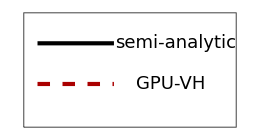

```mathematica
legend=Graphics[{White,EdgeForm[Directive[Thin,Lighter[Black]]],Rectangle[{-.09,.15},{1.3,0.6}],EdgeForm[],Opacity[1],myLegendItem[Black,0,Null,3,Style["semi-analytic",18],0.48,0.18],myLegendItem[Darker[Red],0,Dashing[Medium],3,Style["GPU-VH",18],0.32,0.15]},ImageSize->{260,140}]
```

## 3d visualization

```mathematica
hbarc=0.197326938;
```

```mathematica
outputDir="/Users/derek/MEGA/plotting/output";
```

```mathematica
t=0.5;
```

```mathematica
eInt=Interpolation[Import[outputDir<>"/e_"<>ToString[PaddedForm[t,{3,3},NumberPadding->{"","0"}]]<>".dat"],InterpolationOrder->3]
```

InterpolatingFunction[{{-5., 5.}, {-5., 5.}, {-2.5, 2.5}}, <>]

```mathematica
edata=Import[outputDir<>"/e_"<>ToString[PaddedForm[t,{3,3},NumberPadding->{"","0"}]]<>".dat"];
```

```mathematica
edata2=Flatten[edata];
```

```mathematica
For[i=1,i≤Length[edata2],i++,
If[NumericQ[N[edata2[[i]]]]==False,Print[i]; Break[];];
];
Print["Done."];
```

Done.

```mathematica
lim=6;
```

```mathematica
eInt=Interpolation[edata,InterpolationOrder->3]
```

InterpolatingFunction[{{-5., 5.}, {-5., 5.}, {-2.5, 2.5}}, <>]

```mathematica
Manipulate[ContourPlot[eInt[x,y,z],{x,-lim,lim},{y,-lim,lim}, PlotLegends->Automatic, PlotTheme->"Scientific", ColorFunction->"TemperatureMap"], {z,-5.0, 5.0}]
```

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,-5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,3.22} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,-1.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,-2.82} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,-5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,-2.92} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,-1.46} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,0.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,1.24} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,4.78} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.3,6.3,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
ContourPlot3D[eInt[x,y,z], {x,-lim,lim},{y,-lim,lim}, {z, -5.0, 5.0}, PlotLegends->Automatic, PlotTheme->"Scientific"]
```

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,-4.99929} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.,-6.,-5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.,-6.,-4.28571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-5.99914,-5.99914,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.14286,-5.14286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

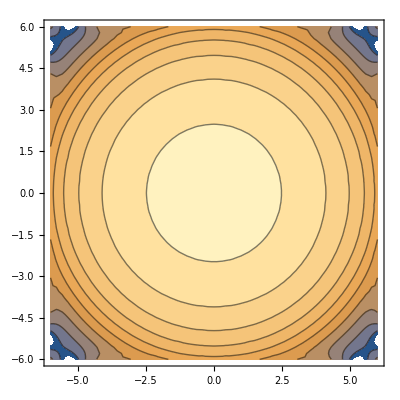

```mathematica
ContourPlot[(eInt[x,y,0]/15.6269)^(1/4)hbarc,{x,-lim,lim},{y,-lim,lim}]
```

```mathematica
(.001/hbarc)^4
```

6.5956×10^-10

```mathematica
1.2/hbarc
```

6.08128

```mathematica
{(.15)^4,(.15)^3}
```

{0.00050625,0.003375}

```mathematica
1/Sqrt[10.^(-8)]
```

10000.

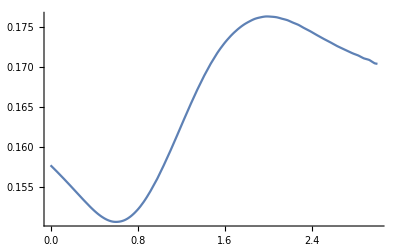

```mathematica
Plot[(eInt[x,0,0]/15.62687363505815)^(1/4)hbarc,{x,0,3}]
```

```mathematica
.15/.197
```

0.761421

```mathematica
.15/.2
```

0.75

```mathematica
(87./14)^(1/4)
```

1.57888

```mathematica
Tanh[0]
```

0

## Equation of state

```mathematica
h0=0.1396;
h1=-.1800;
h2=0.0350;
f0=2.76;
f1=6.79;
f2=-5.29;
g1=-0.47;
g2=1.04;
a=0.01;
```

```mathematica
I4t[t_]:=(h0/(1+a*t^2)+f0*(Tanh[f1*t+f2]+1)/(1+g1*t+g2*t^2))Exp[-h1/t-h2/t^2]
```

```mathematica
I4[T_]:=I4t[T]
```

```mathematica
Peq[T_]:=T^4NIntegrate[I4[x]/x,{x,0,T},AccuracyGoal->20]
```

```mathematica
Clear[h0,h1,h2,f0,f1,f2,g1,g2,a]
```

```mathematica
Integrate[(h0/(1+a*t^2)+f0*(Tanh[f1*t+f2]+1)/(1+g1*t+g2*t^2))Exp[-h1/t-h2/t^2]/t,{t,0,T},Assumptions->{T>0,Element[{h0,h1,h2,f0,f1,f2,g1,g2,a},Reals]}]
```

$Aborted

```mathematica
log10Data=Table[{Log10[T],Log10[Peq[T]]},{T,0.01,5,.01}];
pLog10Int=Interpolation[log10Data]
```

InterpolatingFunction[{{-2., 0.69897}}, <>]

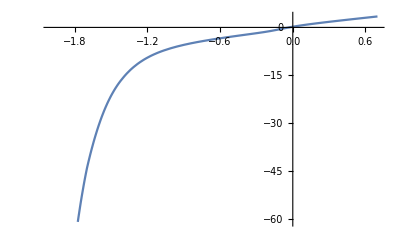

```mathematica
Plot[pLog10Int[t],{t,-2,0.699}]
```

```mathematica
data=Table[{T,Peq[T]},{T,0,5,.01}];
pInt=Interpolation[data,InterpolationOrder->3]
```

InterpolatingFunction[{{0., 5.}}, <>]

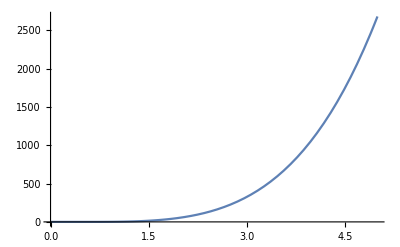

```mathematica
Plot[pInt[T],{T,0,5}]
```

```mathematica
Fit[data,{1,T,T^2,T^3},T]
```

-12.5162+0.178092 T-0.000641348 T^2+7.15954×10^-7 T^3

```mathematica
FindFit[data,h Log10[b+c *T],{h,b,c},T]
```

FindFit::nrlnum: The function value {150.536-3.34588 ⅈ,37.4835-3.34588 ⅈ,16.6439-3.34588 ⅈ,9.21017-3.34588 ⅈ,5.65846-3.34588 ⅈ,3.65073-3.34588 ⅈ,2.38541-3.34588 ⅈ,1.52655-3.34588 ⅈ,«35»,-4.45752+0. ⅈ,-4.55631+0. ⅈ,-4.65203+0. ⅈ,-4.74496+0. ⅈ,-4.83531+0. ⅈ,-4.9233+0. ⅈ,-5.00914+0. ⅈ,«450»} is not a list of real numbers with dimensions {500} at {h,b,c} = {-2.45231,-494.238,22.0153}.

{h→-2.45231,b→-494.238,c→22.0153}

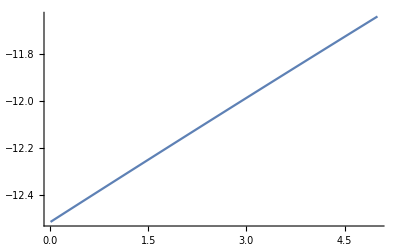

```mathematica
Plot[-12.516164292711158+0.17809185811630335 T-0.000641348202498587 T^2+7.159537980387398*^-7 T^3,{T,.01,5}]
```

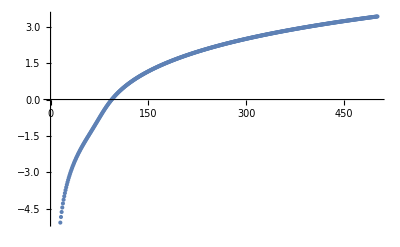

```mathematica
ListPlot[data]
```

```mathematica
InterpolatingPolynomial[data,x]
```

Indeterminate

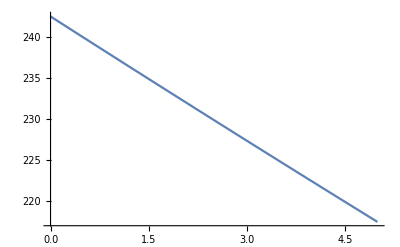

```mathematica
Plot[242.54090781733126-5.1082010512580105 T+0.018644770382451308 T^2,{T,0,5}]
```

```mathematica
eg=16Pi^2/30;
eq=6*3*7Pi^2/120 ;
sFac = eg+eq ;
```

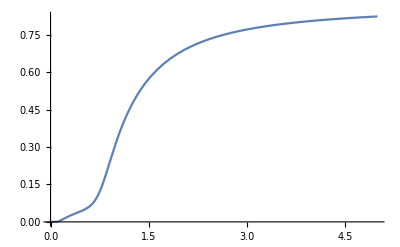

```mathematica
Plot[Peq[T]/(sFac T^4/3),{T,0,5}]
```

```mathematica
f[e_]:=e-M0+M2/(M0+P[e])
```

```mathematica
D[f[e],e]
```

1-(M2 P'[e])/(M0+P[e])^2

## EoS

```mathematica
eosDir ="/home/bazow/Documents/vHydro1p1b-dennis/input/eos/eos-realistic/";
```

```mathematica
eg=16Pi^2/30;
eq=6*3*7Pi^2/120 ;
sFac = eg+eq ;
```

```mathematica
sFac//N
```

15.6269

```mathematica
eosDataRaw=Import[eosDir<>"eosData.dat"];
eosData= Take[eosDataRaw,{3,Length[eosDataRaw]}];
LogEDLogTInt = Interpolation[eosData[[All,{1,2}]]];
edInt[T_] = 10^LogEDLogTInt[Log[10,T]];
LogPLogTInt = Interpolation[eosData[[All,{1,4}]]];
PInt[T_] = 10^LogPLogTInt[Log[10,T]];
```

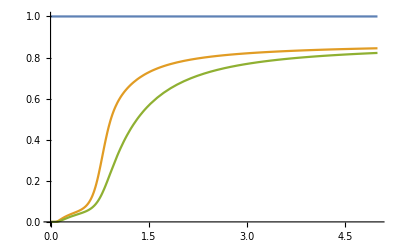

```mathematica
Plot[{1,edInt[T]/(sFac T^4),PInt[T]/(sFac T^4/3)},{T,0,5},FrameLabel->{"T [1/fm]","ℰ/ℰ_ideal, P/P_ideal"}]
```

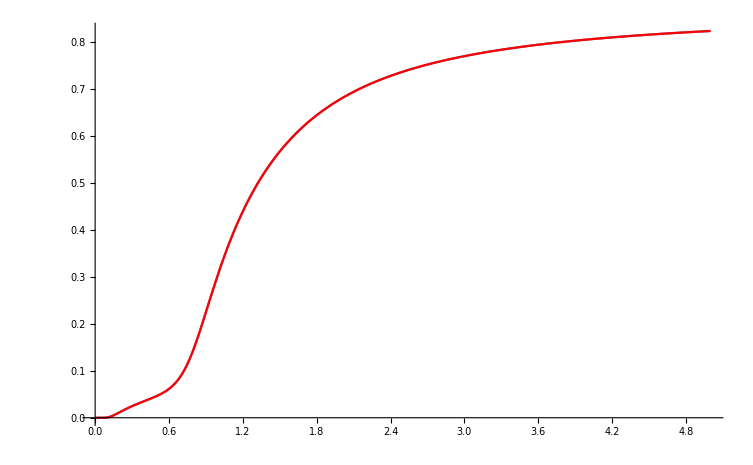

```mathematica
PeqPsbData=Table[{T,PInt[T]/(sFac T^4/3)},{T,0.01,5,0.01}];
Show[Plot[PInt[T]/(sFac T^4/3),{T,0,5}],ListPlot[PeqPsbData,Joined->True,PlotStyle->{Red}]]
```

```mathematica
pLogData=Table[{T,Log[10,PInt[T]]},{T,0.01,5,0.01}];
```

```mathematica
NN=10;
MM=10;
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[PeqPsbData,Sum[a[n]T^n,{n,0,NN}]/Sum[b[m]T^m,{m,0,MM}],vars,T];
varsc=varsa/.sol;
varsd=varsb/.sol;
Q[T_]=Sum[varsc[[n+1]]T^n,{n,0,NN}]/Sum[varsd[[m+1]]T^m,{m,0,MM}]
```

(6.97167×10^-7-0.000109321 T+0.00542582 T^2-0.114807 T^3+1.10858 T^4-4.85226 T^5+12.3856 T^6-20.18 T^7+21.1136 T^8-13.0959 T^9+3.72337 T^10)/(0.00620428-0.0776137 T+0.568208 T^2-0.879151 T^3+0.489387 T^4-2.64158 T^5+11.0096 T^6-20.6782 T^7+22.262 T^8-14.0086 T^9+4.25536 T^10)

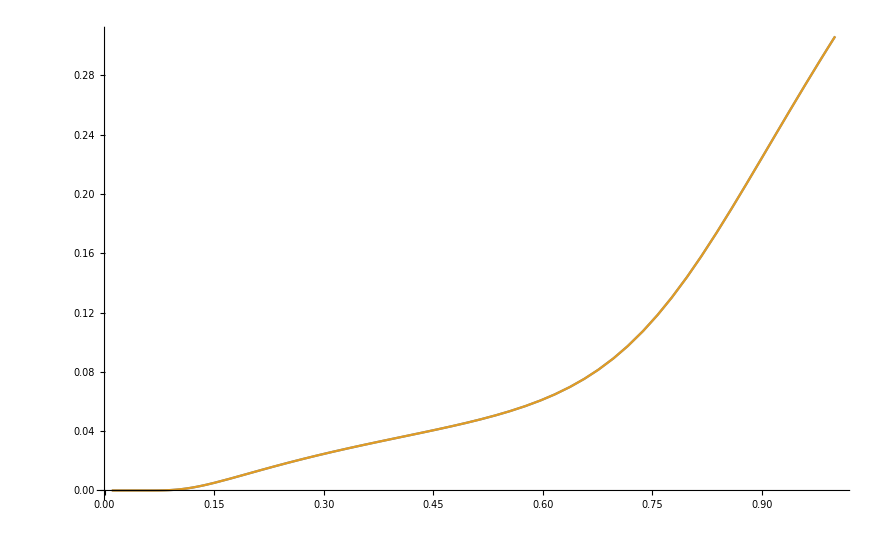

```mathematica
Plot[{PInt[T]/(sFac T^4/3),Q[T]},{T,0.01,1}]
```

```mathematica
Max[Abs[Table[PInt[T]/(sFac T^4/3)-Q[T],{T,0.01,5,0.01}]]]
```

0.0000153472

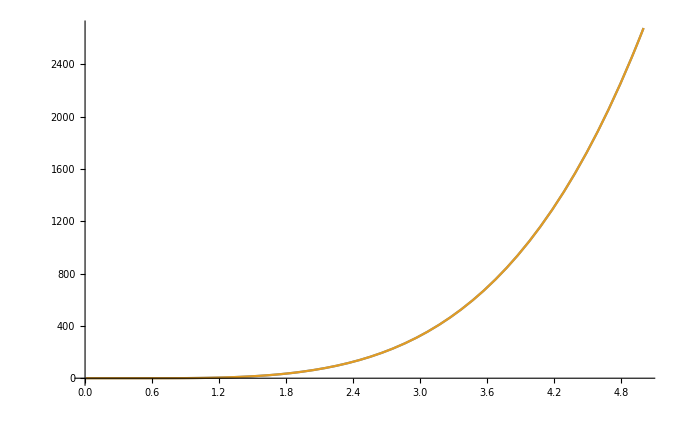

```mathematica
Plot[{PInt[T],Q[T](sFac T^4/3)},{T,0.01,5}]
```

```mathematica
Max[Abs[Table[PInt[T]-Q[T](sFac T^4/3),{T,0.01,5,0.01}]]]
```

0.00473376

### approximate Peq not Peq/P_SB

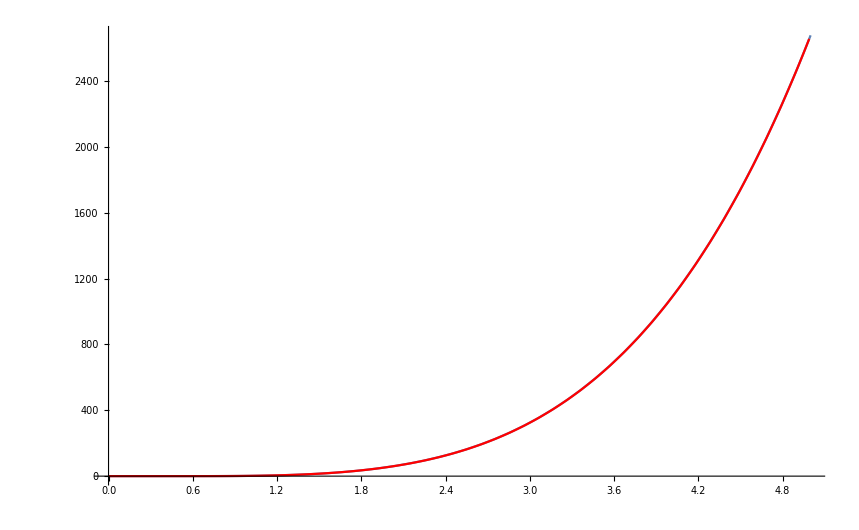

```mathematica
PeqPsbData=Table[{T,PInt[T]},{T,0.0001,5,0.01}];
Show[Plot[PInt[T],{T,0,5}],ListPlot[PeqPsbData,Joined->True,PlotStyle->{Red}]]
```

```mathematica
NN=12;
MM=12;
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[PeqPsbData,Sum[a[n]T^n,{n,0,NN}]/Sum[b[m]T^m,{m,0,MM}],vars,T,AccuracyGoal->20,PrecisionGoal->20];
varsc=varsa/.sol;
varsd=varsb/.sol;
Q[T_]=Sum[varsc[[n+1]]T^n,{n,0,NN}]/Sum[varsd[[m+1]]T^m,{m,0,MM}]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

(0.0000775382-0.0132516 T+0.4902 T^2-7.85013 T^3+67.9227 T^4-357.39 T^5+1259.19 T^6-3096.59 T^7+5345.06 T^8-6349.45 T^9+4944.7 T^10-2274.71 T^11+469.402 T^12)/(18.934-140.293 T+488.311 T^2-1052.18 T^3+1551.18 T^4-1614.08 T^5+1158.23 T^6-520.598 T^7+112.108 T^8-1.23573 T^9+0.106394 T^10-0.00534774 T^11+0.000124809 T^12)

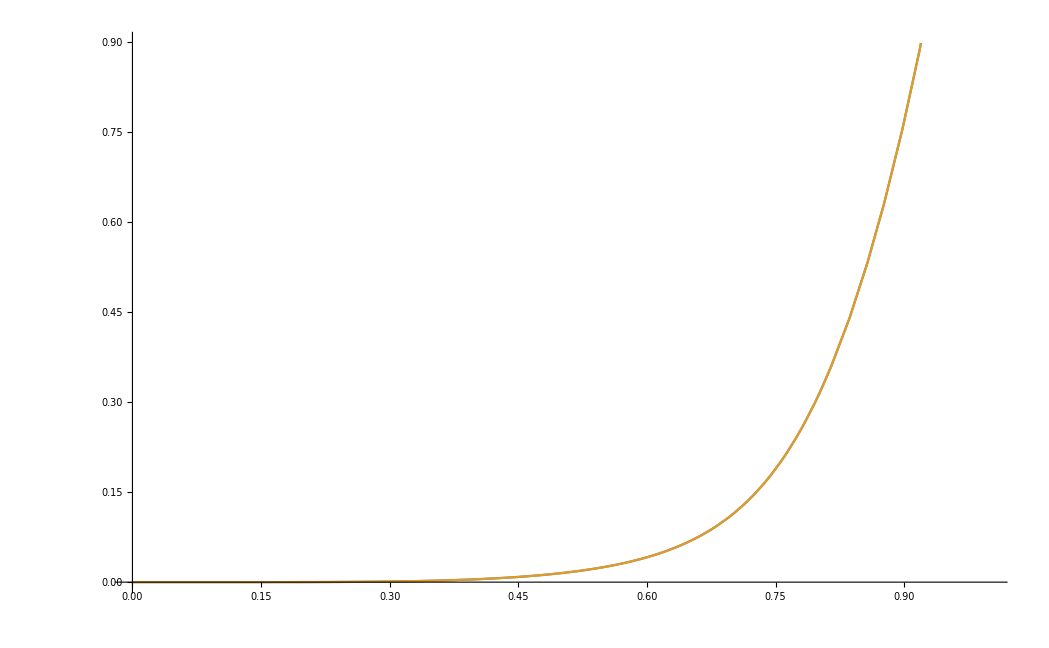

```mathematica
Plot[{PInt[T],Q[T]},{T,0.0001,1}]
```

```mathematica
Max[Abs[Table[PInt[T]-Q[T],{T,0.0001,5,0.001}]]]
```

0.000028483

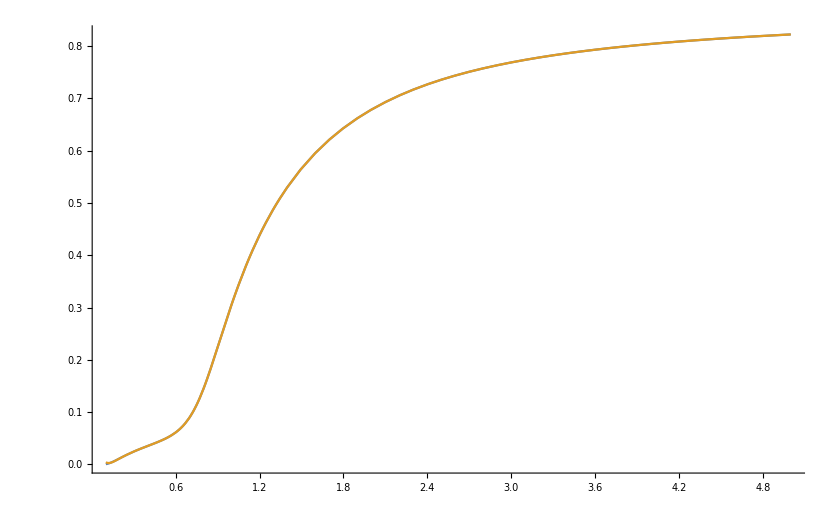

```mathematica
Plot[{PInt[T]/(sFac T^4/3),Q[T]/(sFac T^4/3)},{T,0.1,5},FrameLabel->{"T [1/fm]","ℰ/ℰ_ideal, P/P_ideal"}]
```

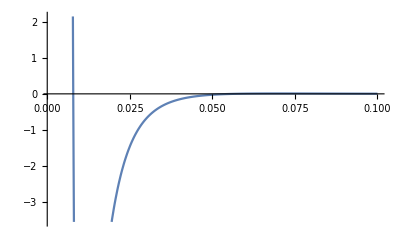

```mathematica
Plot[Q[T]/(sFac T^4/3),{T,0.001,0.1}]
```

```mathematica
(108./13)^(1/4)
```

1.69774

```mathematica
(3000./13)^(1/4)
```

3.89757

```mathematica
{.155,.18}/.2
```

{0.775,0.9}

### speed of sound (cs2=dp/de)

```mathematica
LogDELogTInt = Interpolation[eosData[[All,{1,3}]]];
deInt[T_] = 10^LogDELogTInt[Log[10,T]];
LogDPLogTInt = Interpolation[eosData[[All,{1,5}]]];
dPInt[T_] = 10^LogDPLogTInt[Log[10,T]];
```

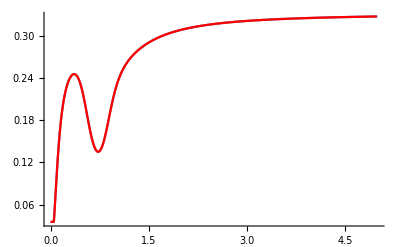

```mathematica
cs2Data=Table[{T,dPInt[T]/deInt[T]},{T,0.0001,5,0.01}];
Show[Plot[dPInt[T]/deInt[T],{T,0,5}],ListPlot[cs2Data,Joined->True,PlotStyle->{Red}]]
```

```mathematica
NN=8;
MM=8;
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[cs2Data,Sum[a[n]T^n,{n,0,NN}]/Sum[b[m]T^m,{m,0,MM}],vars,T,AccuracyGoal->20,PrecisionGoal->20];
varsc=varsa/.sol;
varsd=varsb/.sol;
Q[T_]=Sum[varsc[[n+1]]T^n,{n,0,NN}]/Sum[varsd[[m+1]]T^m,{m,0,MM}]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

(0.0122395-0.0535337 T-7.12789 T^2+174.53 T^3-677.073 T^4+979.192 T^5-420.819 T^6-238.614 T^7+194.161 T^8)/(0.352023-5.42164 T+62.8774 T^2+121.289 T^3-1131.14 T^4+1963.57 T^5-798.537 T^6-785.888 T^7+591.463 T^8)

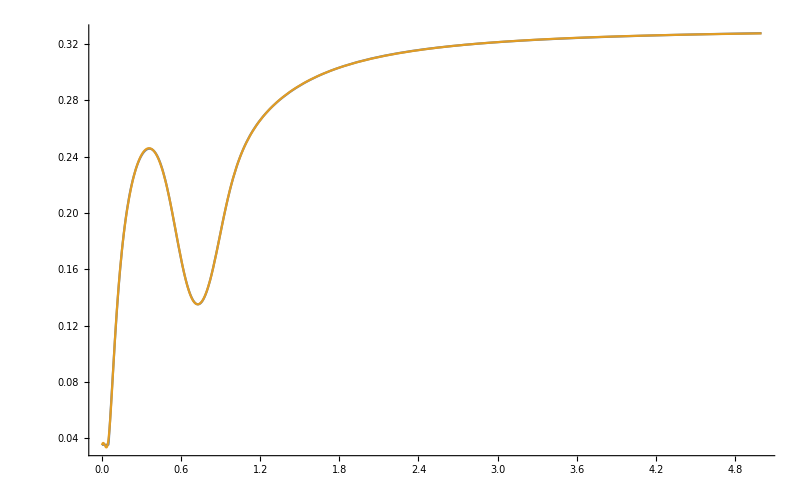

```mathematica
Plot[{dPInt[T]/deInt[T],Q[T]},{T,0.001,5}]
```

```mathematica
Max[Abs[Table[dPInt[T]/deInt[T]-Q[T],{T,0.001,5,0.001}]]]
```

0.00355499

### e vs T

```mathematica
95*Pi^2/180.*3
```

15.6269

```mathematica
.154/0.197326938
```

0.780431

```mathematica
pid=5.20896;
Tc=0.780431;
ct=3.8706;
an=-8.7704;
bn= 3.9200;
cn= 0;
dn= 0.3419;
t0= 0.9761;
ad=-1.2600;
bd=0.8425;
cd= 0;
dd=-0.0475;
```

```mathematica
p[tb_]:=Tc^4*tb^4(1+Tanh[ct*(tb-t0)])*(pid+an/tb+bn/tb^2+cn/tb^3+dn/tb^4)/(1+ad/tb+bd/tb^2+cd/tb^3+dd/tb^4)/2
```

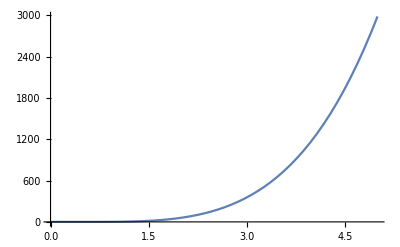

```mathematica
Plot[p[T/Tc],{T,0,5}]
```

```mathematica
dpdtb=D[p[tb],tb];
```

```mathematica
dpdtb//PowerExpand//Simplify//CForm
```

(Power(tb,3)*(-0.012049270492356032 - 0.10036548374421744*Power(tb,2) + 0.46099695367934546*Power(tb,3) + 2.0831775844453166*Power(tb,4) - 
       9.601226952501978*Power(tb,5) + 14.537196726167105*Power(tb,6) - 10.967273045809243*Power(tb,7) + 3.8647291774364856*Power(tb,8) + 
       (-0.011659476591928314*tb + 0.07312242333063487*Power(tb,3) - 0.010194705599075248*Power(tb,4) + 2.4388854511376934*Power(tb,5) - 
          8.850915608328648*Power(tb,6) + 13.898724148878415*Power(tb,7) - 11.008623325324095*Power(tb,8) + 3.7397051885464148*Power(tb,9))*
        Power(Sech(3.8706*(-0.9761 + tb)),2) + (-0.012049270492356032 - 0.10036548374421744*Power(tb,2) + 0.46099695367934546*Power(tb,3) + 
          2.0831775844453166*Power(tb,4) - 9.601226952501978*Power(tb,5) + 14.537196726167105*Power(tb,6) - 10.967273045809243*Power(tb,7) + 
          3.8647291774364856*Power(tb,8))*Tanh(3.8706*(-0.9761 + tb))))/Power(-0.0475 + 0.8425*Power(tb,2) - 1.26*Power(tb,3) + Power(tb,4),2)

```mathematica
Expand[cs2]//PowerExpand//Simplify//CForm
```

(Power(tb,3)*(-0.012049270492356032 - 0.10036548374421747*Power(tb,2) + 0.46099695367934546*Power(tb,3) + 2.0831775844453166*Power(tb,4) - 
       9.601226952501978*Power(tb,5) + 14.537196726167105*Power(tb,6) - 10.967273045809243*Power(tb,7) + 3.8647291774364856*Power(tb,8) + 
       (-0.011659476591928314*tb + 0.07312242333063487*Power(tb,3) - 0.010194705599075248*Power(tb,4) + 2.4388854511376934*Power(tb,5) - 
          8.850915608328648*Power(tb,6) + 13.898724148878415*Power(tb,7) - 11.008623325324095*Power(tb,8) + 3.7397051885464148*Power(tb,9))*
        Power(Sech(3.8706*(-0.9761 + tb)),2) + (-0.012049270492356032 - 0.10036548374421747*Power(tb,2) + 0.46099695367934546*Power(tb,3) + 
          2.0831775844453166*Power(tb,4) - 9.601226952501978*Power(tb,5) + 14.537196726167105*Power(tb,6) - 10.967273045809243*Power(tb,7) + 
          3.8647291774364856*Power(tb,8))*Tanh(3.8706*(-0.9761 + tb))))/Power(-0.0475 + 0.8425*Power(tb,2) - 1.26*Power(tb,3) + Power(tb,4),2)

```mathematica
Nf=2.5;
Nc=3;
(Nc^2-1+7*Nc*Nf/4)*Pi^2/45.*3
```

13.8997

```mathematica
3*(2*(Nc^2-1)+7/2*Nc*Nf)*Pi^2/90.
```

13.8997

```mathematica
LogEDLogTInt = Interpolation[eosData[[All,{1,2}]]];
edInt[T_] = 10^LogEDLogTInt[Log[10,T]];
LogTLogTInt = Interpolation[eosData[[All,{1,1}]]];
TInt[T_] = 10^LogTLogTInt[Log[10,T]];
```

```mathematica
LogTLogTInt
```

InterpolatingFunction[{{-9., 4.}}, <>]

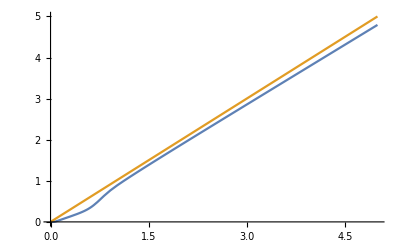

```mathematica
Plot[{(edInt[T]/15.6269)^(1/4),TInt[T]},{T,0,5}]
```